```mathematica
s=0.05;
p=10;
x0=0.5;
ci=1/x0+p-1;
b=1;
c=3;
k=100;
a=(1+p*0.5)*(1+s*0.5*(b-c));
```

```mathematica
acca=NDSolve[{D[n[t],t]==(1+1/(ci*Exp[s*t]-p+1)*(p+s*b-s*c)+(b-c)*p*s/((ci*Exp[s*t]-p+1)^2)-n[t]/k)*n[t],n[0]==4},n[t],{t,0,50}] (*So this is the full one*)
```

{{n[t]→InterpolatingFunction[{{0.,50.}},<>][t]}}

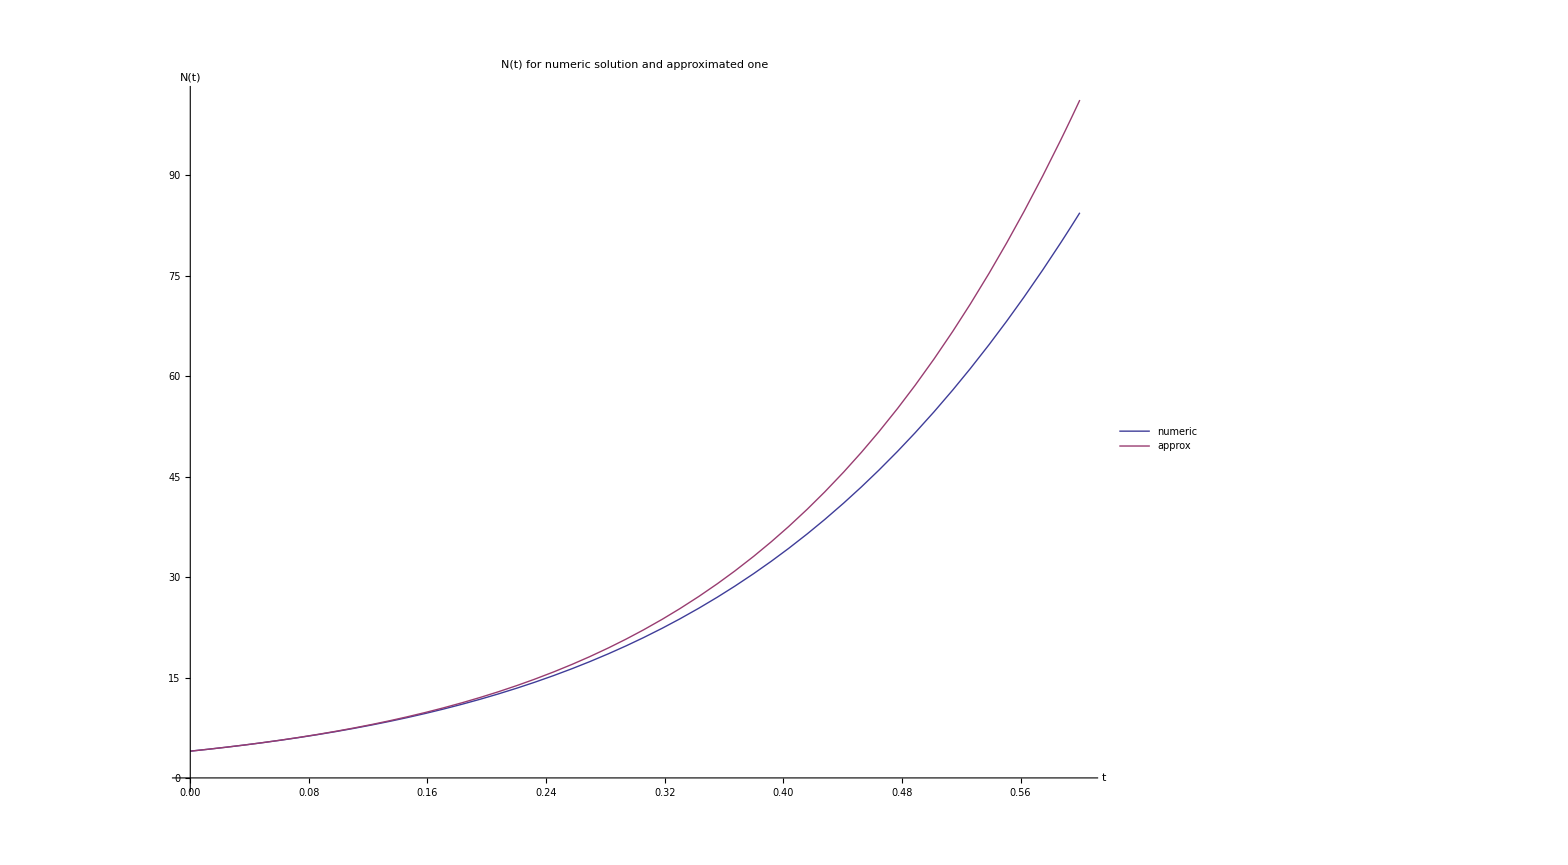

```mathematica
Plot[{Evaluate[n[t]/.acca],a*k*4*Exp[a*t]/(a*k+4*(Exp[a*t]-1))},{t,0,0.6},PlotLegends->Placed[{"numeric","approx"},{0.65,0.8}],AxesLabel->{"t","N(t)"},PlotLabel->"N(t) for numeric solution and approximated one",ImageSize->1400]
```